Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];

CalculateSMatrix2[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_,nGrid_]:= Module[{y,x,L,RHS,RHS2,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t,sTable,s,time1,dT,time2},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
L = 1/2*u^2;
Af = Grad[fx,xState]; (* For nD stuff use Grad*)
Bf = D[fx,u] ;(*For 1D stuff use D*)
Q = Grad[Grad[L,xState],xState]; (* Fix this *)
Mf = Grad[D[L,u],xState];
R = D[L,{u,2}];
S0 = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
RHS[i_] :=(IdentityMatrix[4] + Afᵀ.Subscript[s, i] + Subscript[s, i].Af - KroneckerProduct[Subscript[s, i].Bf,Bfᵀ.Subscript[s, i]]) /. {x-> x1a[τ - i*τ/nGrid], xdot -> xdot1a[τ - i*τ/nGrid], θ ->θ1a[τ - i*τ/nGrid], θdot -> θdot1a[τ - i*τ/nGrid], u -> u1a[τ - i*τ/nGrid]}; 
Subscript[s, 0] = S0;
dT = τ/nGrid;
sTable = Table[Subscript[s, i+1] = Subscript[s, i] + dT*RHS[i],{i,0,nGrid}];
sTable
]
CalculateSMatrix[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,τ_,A_]:=Module[{x,L,RHS,xdot,θ,θdot,u,K,S,soltn,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},xState={x,xdot,θ,θdot};x2dot=(u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2);θ2dot=(-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]))/(1-A Cos[θ]^2);fx={xdot,x2dot,θdot,θ2dot};L=u^2/2;Af=fxxState;Bf=D[fx, u];Q=LxStatexState;Mf=D[L, u]xState;R=D[L, {u,2}];S0={{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};RHS[t_]:=IdentityMatrix[4]+Transpose[Af].S[t]+S[t].Af-KroneckerProduct[S[t].Bf,Transpose[Bf].S[t]]/.{x->x1a[τ-t],xdot->xdot1a[τ-t],θ->θ1a[τ-t],θdot->θdot1a[τ-t],u->u1a[τ-t]};sol2=S/.NDSolve[{S'[t]==RHS[t],S[0]==S0},S,{t,0,τ}];S=sol2⟦1⟧]
CalculateGains2[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,sTable_,nGrid_]:= Module[{index,x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
index = Round[τ - time,τ/nGrid]/(τ/nGrid);
K = (Bfᵀ.Indexed[sTable,1+index])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]
CalculateGains[x1a_,xdot1a_,θ1a_,θdot1a_,u1a_,time_,A_,τ_,S_]:= Module[{x,L,RHS,xdot,θ,θdot,u,K,Af,Bf,Q,fx,xState,R,Mf,x2dot,θ2dot,S0,sol2,t},
xState = {x,xdot,θ,θdot};
x2dot = 1/(1-A Cos[θ]^2) (u+A θdot^2 Sin[θ]+A Cos[θ] Sin[θ]);
θ2dot= 1/(1-A Cos[θ]^2) (-Sin[θ]-Cos[θ] (u+A θdot^2 Sin[θ]));
fx = {xdot,x2dot,θdot,θ2dot};
Bf = D[fx,u] ;(*For 1D stuff use D*)
K = (Bfᵀ.S[τ - time])/. {x-> x1a[time], xdot -> xdot1a[time], θ ->θ1a[time], θdot -> θdot1a[time], u -> u1a[time]};
K
]

ffCartPendulum[ICs_,n_?NumericQ,τ_?NumericQ,τ1_?NumericQ,A_?NumericQ,order_?NumericQ,maxIter_?NumericQ,maxError_?NumericQ,uMax_?NumericQ,maxCount_?NumericQ,initGuess_,maxJ_?NumericQ]:=
Module[{frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess = Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
	xdot,
	1/(1-A Cos[θ]^2) (A θdot^2 Sin[θ]+1/(1-A Cos[θ]^2) (λ4 Cos[θ]-λ2)+A Cos[θ] Sin[θ]),
	θdot,
	1/(1-A Cos[θ]^2) (-(1/(1-A Cos[θ]^2))(-λ2 Cos[θ]+λ4 Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ]),
	0,
	-λ1,
	1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
	4 /(A Cos[2 θ]+A-2) (A θdot Sin[θ] (λ2-λ4 Cos[θ]))-λ3
};

InitGuess = initGuess;
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];

bcs={Subscript[x, 0]==ICs[[1]],Subscript[xdot, 0]==ICs[[2]],Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs[[3]],Subscript[θdot, 0]==ICs[[4]],Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==
1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+
f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+
{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];

sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

froot=FindRoot[eqns,sv,MaxIterations->maxIter];
error = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];

count = 0;

(*Print["Error First Guess = ",error];*)

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
While[((error > maxError) || (J > maxJ)) && count <= maxCount ,
InitGuess = {RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess = Table[If[i != -1,Subscript[xGuess, i+1] = Subscript[xGuess, i] +Δt*f[Subscript[xGuess, i]],Subscript[xGuess, 0] = {ICs[[1]],ICs[[2]],ICs[[3]],ICs[[4]],InitGuess[[1]],InitGuess[[2]],InitGuess[[3]],InitGuess[[4]]}],{i,-1,n-1}];
sv = Flatten[Table[{{Subscript[x, i],xGuess[[i+1]][[1]]},{Subscript[xdot, i],xGuess[[i+1]][[2]]},{Subscript[θ, i],xGuess[[i+1]][[3]]},{Subscript[θdot, i],xGuess[[i+1]][[4]]},
					{Subscript[λ1, i],xGuess[[i+1]][[5]]},{Subscript[λ2, i],xGuess[[i+1]][[6]]},{Subscript[λ3, i],xGuess[[i+1]][[7]]},{Subscript[λ4, i],xGuess[[i+1]][[8]]}},{i,0,n}],1];

frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew = Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]} - {0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]} - ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew <= error,froot = frootNew;error = errorNew;
uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
,_];
count = count+1;

(*Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];*)

];


xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ1ff0 = ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ2ff0 = ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ3ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];
λ4ff0 = ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

uff0=ListInterpolation[Table[1/(1-A Cos[Subscript[θ, i]]^2) (Subscript[λ4, i]Cos[Subscript[θ, i]]-Subscript[λ2, i]),{i,0,n}]/. froot,{0,τ},InterpolationOrder->order];

xff[t_]:=Piecewise[{{xff0[t],0<=t<=τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0<=t<=τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0<=t<=τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0<=t<=τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0<=t<=τ}},0];
J = NIntegrate[uff0[t]^2,{t,0,τ}];
S = CalculateSMatrix[xff,xdotff,θff,θdotff,uff,τ,A];
K[time_] := CalculateGains[xff,xdotff,θff,θdotff,uff,time,A,τ,S];
{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]
ffCartPendulum2[ICs_,n_,τ_,τ1_,A_,order_,maxIter_,maxError_,uMax_,maxCount_,initGuess_,maxJ_,nGrid_]:=
Module[{time1,time2,sTable,frootNew,errorNew,InitGuess,J,S,K,count,error,x,dist,xdot,f,θ,θdot,λ1,λ2,λ3,λ4,Δt,bcs,eqns,sv,froot,xff,xdotff,xff0,xdotff0,θff0,θdotff0,uff0,
θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,i,xGuess=Table[Subscript[xGuess, i],{i,0,n}]},Δt=τ/n;
f[{x_,xdot_,θ_,θdot_,λ1_,λ2_,λ3_,λ4_}]:={
xdot,(A θdot^2 Sin[θ]+(λ4 Cos[θ]-λ2)/(1-A Cos[θ]^2)+A Cos[θ] Sin[θ])/(1-A Cos[θ]^2),θdot,(-(-λ2 Cos[θ]+λ4 Cos[θ]^2)/(1-A Cos[θ]^2)-Sin[θ]-A θdot^2 Cos[θ] Sin[θ])/(1-A Cos[θ]^2),
0,-λ1,1/((-1+A Cos[θ]^2)^3)(A^2 (A θdot^2 λ2-λ4) Cos[θ]^5+A^3 (λ2-θdot^2 λ4) Cos[θ]^6-1/2 A^2 (λ2-θdot^2 λ4) Cos[θ]^4 (4-A+A Cos[2 θ])-A Cos[θ]^2 (-λ2+θdot^2 λ4+3 λ2 λ4 Sin[θ])+Cos[θ] (A θdot^2 λ2-λ4+(2 A λ2^2+λ4^2) Sin[θ]-2 A^2 θdot^2 λ2 Sin[θ]^2)+A Cos[θ]^3 (-2 A θdot^2 λ2+2 λ4+λ4^2 Sin[θ]+2 A (A θdot^2 λ2-λ4) Sin[θ]^2)+Sin[θ] (-λ2 λ4-A (λ2-θdot^2 λ4) Sin[θ]+A λ4 Sin[2 θ])),
(4 (A θdot Sin[θ] (λ2-λ4 Cos[θ])))/(A Cos[2 θ]+A-2)-λ3};
InitGuess=initGuess;
xGuess=Table[If[i≠-1,Subscript[xGuess, i+1]=Subscript[xGuess, i]+Δt f[Subscript[xGuess, i]],
Subscript[xGuess, 0]={ICs⟦1⟧,ICs⟦2⟧,ICs⟦3⟧,ICs⟦4⟧,InitGuess⟦1⟧,InitGuess⟦2⟧,InitGuess⟦3⟧,InitGuess⟦4⟧}],{i,-1,n-1}];
bcs={Subscript[x, 0]==ICs⟦1⟧,Subscript[xdot, 0]==ICs⟦2⟧,Subscript[x, n]==Subscript[xdot, n]==0,Subscript[θ, 0]==ICs⟦3⟧,Subscript[θdot, 0]==ICs⟦4⟧,Subscript[θdot, n]==0,Subscript[θ, n]==π};
eqns=Flatten[Join[bcs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}==1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}],{i,1,n}]]];
sv=Flatten[Table[{{Subscript[x, i],xGuess⟦i+1⟧⟦1⟧},{Subscript[xdot, i],xGuess⟦i+1⟧⟦2⟧},{Subscript[θ, i],xGuess⟦i+1⟧⟦3⟧},{Subscript[θdot, i],xGuess⟦i+1⟧⟦4⟧},{Subscript[λ1, i],xGuess⟦i+1⟧⟦5⟧},{Subscript[λ2, i],xGuess⟦i+1⟧⟦6⟧},{Subscript[λ3, i],xGuess⟦i+1⟧⟦7⟧},{Subscript[λ4, i],xGuess⟦i+1⟧⟦8⟧}},{i,0,n}],1];
{time1,froot}=Timing[FindRoot[eqns,sv,MaxIterations->maxIter]];
error=Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]}-{0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]}-ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.froot,"Frobenius"];
count=0;uff0=ListInterpolation[Table[(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i])/(1-A Cos[Subscript[θ, i]]^2),{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
J=NIntegrate[uff0[t]^2,{t,0,τ}];
While[(error>maxError||J>maxJ)&&count≤maxCount,
InitGuess={RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}],RandomReal[{-1,1}]};
xGuess=Table[If[i≠-1,Subscript[xGuess, i+1]=Subscript[xGuess, i]+Δt f[Subscript[xGuess, i]],Subscript[xGuess, 0]={ICs⟦1⟧,ICs⟦2⟧,ICs⟦3⟧,ICs⟦4⟧,InitGuess⟦1⟧,InitGuess⟦2⟧,InitGuess⟦3⟧,InitGuess⟦4⟧}],{i,-1,n-1}];
sv=Flatten[Table[{{Subscript[x, i],xGuess⟦i+1⟧⟦1⟧},{Subscript[xdot, i],xGuess⟦i+1⟧⟦2⟧},{Subscript[θ, i],xGuess⟦i+1⟧⟦3⟧},{Subscript[θdot, i],xGuess⟦i+1⟧⟦4⟧},{Subscript[λ1, i],xGuess⟦i+1⟧⟦5⟧},{Subscript[λ2, i],xGuess⟦i+1⟧⟦6⟧},{Subscript[λ3, i],xGuess⟦i+1⟧⟦7⟧},{Subscript[λ4, i],xGuess⟦i+1⟧⟦8⟧}},{i,0,n}],1];
frootNew=FindRoot[eqns,sv,MaxIterations->maxIter];
errorNew=Norm[Flatten[Join[{Subscript[x, n],Subscript[xdot, n],Subscript[θ, n],Subscript[θdot, n]}-{0,0,π,0},{Subscript[x, 0],Subscript[xdot, 0],Subscript[θ, 0],Subscript[θdot, 0]}-ICs,Table[Thread[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}-(1/2 Δt (f[{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]}]+f[{Subscript[x, i],Subscript[xdot, i],Subscript[θ, i],Subscript[θdot, i],Subscript[λ1, i],Subscript[λ2, i],Subscript[λ3, i],Subscript[λ4, i]}])+{Subscript[x, i-1],Subscript[xdot, i-1],Subscript[θ, i-1],Subscript[θdot, i-1],Subscript[λ1, i-1],Subscript[λ2, i-1],Subscript[λ3, i-1],Subscript[λ4, i-1]})],{i,1,n}]]]/.frootNew,"Frobenius"];
If[errorNew≤error,froot=frootNew;error=errorNew;uff0=ListInterpolation[Table[(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i])/(1-A Cos[Subscript[θ, i]]^2),{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
J=NIntegrate[uff0[t]^2,{t,0,τ}];,_];
count=count+1;
(*Print["Count Shooting= ",count,"    Error New = ",errorNew,"    Error Min = ",error];*)
];
xff0=ListInterpolation[Table[Subscript[x, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
xdotff0=ListInterpolation[Table[Subscript[xdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
θff0=ListInterpolation[Table[Subscript[θ, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
θdotff0=ListInterpolation[Table[Subscript[θdot, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ1ff0=ListInterpolation[Table[Subscript[λ1, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ2ff0=ListInterpolation[Table[Subscript[λ2, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ3ff0=ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
λ4ff0=ListInterpolation[Table[Subscript[λ3, i],{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
uff0=ListInterpolation[Table[(Subscript[λ4, i] Cos[Subscript[θ, i]]-Subscript[λ2, i])/(1-A Cos[Subscript[θ, i]]^2),{i,0,n}]/.froot,{0,τ},InterpolationOrder->order];
xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];
xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];
θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];
θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];
uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];
J=NIntegrate[uff0[t]^2,{t,0,τ}];
sTable=CalculateSMatrix2[xff,xdotff,θff,θdotff,uff,τ,A,nGrid];
K[time_]:=CalculateGains2[xff,xdotff,θff,θdotff,uff,time,A,τ,sTable,nGrid];{xff,xdotff,θff,θdotff,uff,λ1ff0,λ2ff0,λ3ff0,λ4ff0,J,K}]

testSwingUp[ICs_,τ_,τ1_,uff0_,A_]:=Module[{eq,init,x,xdot,θ,θdot,xs,xdots,θs,θdots,t,J},eq={x'[t]==xdot[t],xdot'[t]==(uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]])/(1-A Cos[θ[t]]^2),θ'[t]==θdot[t],θdot'[t]==(-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))/(1-A Cos[θ[t]]^2)};init={x[0]==ICs⟦1⟧,xdot[0]==ICs⟦2⟧,θ[0]==ICs⟦3⟧,θdot[0]==ICs⟦4⟧};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];J=NIntegrate[uff0[t]^2,{t,0,τ}];{xs,xdots,θs,θdots,uff0,J}]

testWithFB[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},κ1=κ2=3;κ3=-0.1;κ4=-0.65;xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];ufb[t_]:=Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0≤t≤τ}},κ1 (θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3 (xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=uff[t]+ufb[t];eq={x'[t]==xdot[t],xdot'[t]==(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]])/(1-A Cos[θ[t]]^2),θ'[t]==θdot[t],θdot'[t]==(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))/(1-A Cos[θ[t]]^2)};init={x[0]==ICs⟦1⟧,xdot[0]==ICs⟦2⟧,θ[0]==ICs⟦3⟧,θdot[0]==ICs⟦4⟧};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];us[t_]:=uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0≤t≤τ}},κ1 (θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3 (xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])];J=NIntegrate[us[t]^2,{t,0,τ}];{xs,xdots,θs,θdots,us,J}]

testWithFBClipped[ICs_,τ_,τ1_,xff0_,xdotff0_,θff0_,θdotff0_,uff0_,A_,uBound_,K_]:=Module[{eq,init,θ,θdot,θff,θdotff,x,xdot,xff,xdotff,uff,t,κ1,κ2,κ3,κ4,ufb,u,θs,θdots,xs,xdots,us,J},κ1=κ2=3;κ3=-0.1;κ4=-0.65;xff[t_]:=Piecewise[{{xff0[t],0≤t≤τ}},0];xdotff[t_]:=Piecewise[{{xdotff0[t],0≤t≤τ}},0];θff[t_]:=Piecewise[{{θff0[t],0≤t≤τ}},π];θdotff[t_]:=Piecewise[{{θdotff0[t],0≤t≤τ}},0];uff[t_]:=Piecewise[{{uff0[t],0≤t≤τ}},0];ufb[t_]:=Piecewise[{{K[t].{xff[t]-x[t],xdotff[t]-xdot[t],θff[t]-θ[t],θdotff[t]-θdot[t]},0≤t≤τ}},κ1 (θff[t]-θ[t])+κ2 (θdotff[t]-θdot[t])+κ3 (xff[t]-x[t])+κ4 (xdotff[t]-xdot[t])];u[t_]:=Clip[uff[t]+ufb[t],{-uBound,uBound}];eq={x'[t]==xdot[t],xdot'[t]==(u[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]])/(1-A Cos[θ[t]]^2),θ'[t]==θdot[t],θdot'[t]==(-Sin[θ[t]]-Cos[θ[t]] (u[t]+A θdot[t]^2 Sin[θ[t]]))/(1-A Cos[θ[t]]^2)};init={x[0]==ICs⟦1⟧,xdot[0]==ICs⟦2⟧,θ[0]==ICs⟦3⟧,θdot[0]==ICs⟦4⟧};{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,τ1},Method->{"DiscontinuityProcessing"->None}];us[t_]:=Clip[uff[t]+Piecewise[{{K[t].{xff[t]-xs[t],xdotff[t]-xdots[t],θff[t]-θs[t],θdotff[t]-θdots[t]},0≤t≤τ}},κ1 (θff[t]-θs[t])+κ2 (θdotff[t]-θdots[t])+κ3 (xff[t]-xs[t])+κ4 (xdotff[t]-xdots[t])],{-uBound,uBound}];J=NIntegrate[us[t]^2,{t,0,τ}];{xs,xdots,θs,θdots,us,J}]

Energy[{x1_,x2_,θ1_,θ2_,A_}] := 1/2*x2^2 + 1/2*A*θ2^2 + A*Cos[θ1]*x2*θ2 - A*Cos[θ1];
```

ICs = {0,-0.442495,0.605262,-0.364812}

Energy Initial = -0.0267107

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$217749 near {t$217749} = {3.21281}. NIntegrate obtained 22.3862 and 0.00132138 for the integral and error estimates.

ff computation time = 8.94025

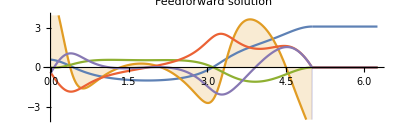
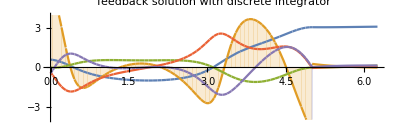
-Graphics- | -Graphics-

```mathematica
n=60;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 5;nGrid = 60;maxJ = 2^2*τ;

xdotMin = -2;
xdotMax = 2;
θMin = -π;
θMax = π;
θdotMin = -2;
θdotMax = 2;

xdotInit = RandomReal[{xdotMin,xdotMax}];
θInit = RandomReal[{θMin,θMax}];
θdotInit = RandomReal[{θdotMin,θdotMax}];
ICs = {0,xdotInit,θInit,θdotInit};
ICs = ICData[[1]];
Print["ICs = ",ICs];
InitGuess = {0,0,0,0};
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
Print["Energy Initial = ",EInitial];
{time2,{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}}=Quiet[RepeatedTiming[ffCartPendulum2[ICs,n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ,nGrid]]]; 
{x1c,xdot1c,θ1c,θdot1c,u1c,J}=testWithFBClipped[ICs,τ,τ1,x1a,xdot1a,θ1a,θdot1a,u1a,A,uMax,K];
Print["ff computation time = ",time2];
p1a = Plot[{θ1a[t],u1a[t],x1a[t],θdot1a[t],xdot1a[t]},{t,0,τ1},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1a","u1a","x1a","θdot1a","xdot1a"},PlotLabel->"Feedforward solution",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
p1c=Plot[{θ1c[t],u1c[t],x1c[t],θdot1c[t],xdot1c[t]},{t,0,τ1},PlotRange->{-4,4},Filling->{2->Axis},PlotLegends->{"θ1c","u1c","x1c","θdot1c","xdot1c"},PlotLabel->"feedback solution with discrete integrator",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}];
Grid[{{p1a,p1c}}]
```

### Define Computation Time function

```mathematica
ComputationTime[ICs_] := Module[{time},
EInitial = Energy[Join[Table[ICs[[i]],{i,1,4}],{A}]];
{time,{x1a,xdot1a,θ1a,θdot1a,u1a,λ1ff0,λ2ff0,λ3ff0,λ4ff0,Jff,K}}=Quiet[Timing[ffCartPendulum2[ICs,n,τ,τ1,A,order,maxIter,maxError,uMax,maxCount,InitGuess,maxJ,nGrid]]]; 
Print["Time Taken = ",time];
time
]

ICData = Import["ICDataComputation20.mx"];
EData = Import["EDataComputation20.mx"];
```

```mathematica
ComputationTime[ICData[[1]]];
```

Time Taken = 8.82813

### Use the above 200 ICData points for all simulations

```mathematica
numberTests = 200;
n=100;τ=5;τ1=τ*1.25;A=0.2;order = 4;maxIter = 100;maxError = 0.01;uMax = 5;maxCount = 10;nGrid = 60;maxJ = 2^2*τ;
InitGuess = {0,0,0,0};
xdotMin = -2;xdotMax = 2;θMin = -π;θMax = π;θdotMin = -2;θdotMax = 2;

TimingData = ParallelTable[ComputationTime[ICData[[i]]],{i,1,numberTests}];

Export["TimingDataComputation100.mx",TimingData];
```

Time Taken = 2.09375

Time Taken = 2.09375

Time Taken = 2.14063

Time Taken = 2.03125

Time Taken = 2.07813

Time Taken = 2.07813

Time Taken = 1.95313

Time Taken = 1.90625

Time Taken = 9.625

Time Taken = 1.98438

Time Taken = 1.95313

Time Taken = 1.95313

Time Taken = 21.7969

Time Taken = 2.10938

Time Taken = 21.0938

Time Taken = 2.01563

Time Taken = 21.5781

Time Taken = 20.6563

Time Taken = 3.95313

Time Taken = 2.10938

Time Taken = 2.04688

Time Taken = 16.4375

Time Taken = 2.07813

Time Taken = 2.17188

Time Taken = 2.01563

Time Taken = 21.2813

Time Taken = 2.14063

Time Taken = 1.90625

Time Taken = 2.1875

Time Taken = 2.26563

Time Taken = 1.82813

Time Taken = 2.09375

Time Taken = 2.01563

Time Taken = 2.04688

Time Taken = 4.4375

Time Taken = 3.54688

Time Taken = 2.125

Time Taken = 1.95313

Time Taken = 1.96875

Time Taken = 20.625

Time Taken = 4.45313

Time Taken = 1.98438

Time Taken = 1.96875

Time Taken = 2.03125

Time Taken = 2.1875

Time Taken = 2.03125

Time Taken = 2.01563

Time Taken = 2.15625

Time Taken = 2.09375

Time Taken = 19.3281

Time Taken = 9.65625

Time Taken = 1.8125

Time Taken = 2.07813

Time Taken = 21.4531

Time Taken = 2.10938

Time Taken = 23.7969

Time Taken = 2.

Time Taken = 9.07813

Time Taken = 20.4219

Time Taken = 2.14063

Time Taken = 22.9688

Time Taken = 2.01563

Time Taken = 1.96875

Time Taken = 20.0156

Time Taken = 23.0313

Time Taken = 1.875

Time Taken = 1.875

Time Taken = 2.01563

Time Taken = 1.96875

Time Taken = 5.8125

Time Taken = 23.2031

Time Taken = 2.03125

Time Taken = 19.7031

Time Taken = 22.5313

Time Taken = 2.

Time Taken = 18.2656

Time Taken = 23.1094

Time Taken = 1.96875

Time Taken = 25.2344

Time Taken = 23.0313

Time Taken = 2.

Time Taken = 1.85938

Time Taken = 12.9844

Time Taken = 1.90625

Time Taken = 2.04688

Time Taken = 2.28125

Time Taken = 21.7188

Time Taken = 2.0625

Time Taken = 21.4063

Time Taken = 1.8125

Time Taken = 2.03125

Time Taken = 1.84375

Time Taken = 2.125

Time Taken = 1.65625

Time Taken = 1.70313

Time Taken = 1.60938

Time Taken = 1.60938

Time Taken = 1.6875

Time Taken = 8.10938

Time Taken = 1.57813

Time Taken = 23.

Time Taken = 2.15625

Time Taken = 2.07813

Time Taken = 2.01563

Time Taken = 2.

Time Taken = 22.8594

Time Taken = 2.03125

Time Taken = 2.04688

Time Taken = 2.10938

Time Taken = 2.09375

Time Taken = 2.0625

Time Taken = 18.3906

Time Taken = 2.23438

Time Taken = 2.14063

Time Taken = 12.6563

Time Taken = 2.20313

Time Taken = 1.84375

Time Taken = 21.625

Time Taken = 3.85938

Time Taken = 2.07813

Time Taken = 1.95313

Time Taken = 2.03125

Time Taken = 1.8125

Time Taken = 1.64063

Time Taken = 21.7188

Time Taken = 21.625

Time Taken = 2.03125

Time Taken = 2.04688

Time Taken = 30.4531

Time Taken = 1.96875

Time Taken = 33.2344

Time Taken = 21.3594

Time Taken = 22.

Time Taken = 2.09375

Time Taken = 10.25

Time Taken = 1.90625

Time Taken = 23.8125

Time Taken = 3.85938

Time Taken = 2.07813

Time Taken = 1.71875

Time Taken = 1.98438

Time Taken = 1.71875

Time Taken = 24.625

Time Taken = 2.125

Time Taken = 3.59375

Time Taken = 7.51563

Time Taken = 22.4844

Time Taken = 2.17188

Time Taken = 2.40625

Time Taken = 2.03125

Time Taken = 4.07813

Time Taken = 15.8906

Time Taken = 4.04688

Time Taken = 18.2813

Time Taken = 5.9375

Time Taken = 21.4688

Time Taken = 19.3438

Time Taken = 24.6563

Time Taken = 1.8125

Time Taken = 2.

Time Taken = 2.0625

Time Taken = 23.1094

Time Taken = 3.98438

Time Taken = 22.4844

Time Taken = 2.03125

Time Taken = 2.125

Time Taken = 2.

Time Taken = 19.8906

Time Taken = 25.125

Time Taken = 22.

Time Taken = 2.01563

Time Taken = 22.0156

Time Taken = 2.03125

Time Taken = 1.9375

Time Taken = 21.5469

Time Taken = 2.

Time Taken = 1.89063

Time Taken = 1.95313

Time Taken = 1.96875

Time Taken = 7.57813

Time Taken = 24.5156

Time Taken = 2.01563

Time Taken = 2.07813

Time Taken = 2.09375

Time Taken = 22.1719

Time Taken = 1.75

Time Taken = 3.67188

Time Taken = 24.1406

Time Taken = 1.71875

Time Taken = 3.54688

Time Taken = 1.71875

Time Taken = 1.75

Time Taken = 1.82813

Time Taken = 1.46875

Time Taken = 18.8594

Time Taken = 1.48438

Time Taken = 5.9375

Time Taken = 17.0313

Time Taken = 1.5625

Time Taken = 16.7969

### Clean up Bad data points

```mathematica
Table[
If[TimingData[[i]]>20,
TimingData[[i]] = ComputationTime[ICData[[i]]];
Print["i = ",i,"    TimingData = ",TimingData[[i]]];
,_];
,{i,162,numberTests}];
```

Time Taken = 16.3594

i = 173    TimingData = 16.3594

Time Taken = 14.9844

i = 174    TimingData = 14.9844

Time Taken = 15.7188

i = 179    TimingData = 15.7188

Time Taken = 16.0625

i = 189    TimingData = 16.0625

$Aborted

```mathematica
Export["TimingDataComputation60.mx",TimingData];
```

### Obtain Previous Data

```mathematica
TimingData20 = Import["TimingDataComputation20.mx"]
```

{1.70313,0.40625,0.453125,0.40625,0.4375,0.390625,0.453125,0.46875,0.421875,1.60938,0.46875,0.421875,0.53125,1.82813,0.421875,1.84375,2.15625,0.5,0.921875,1.625,0.453125,0.46875,0.5,0.453125,1.65625,0.4375,0.609375,0.484375,0.421875,0.453125,1.1875,0.4375,0.390625,0.328125,1.79688,1.92188,1.9375,0.46875,1.84375,0.390625,1.39063,1.17188,1.53125,0.46875,0.390625,0.515625,0.625,0.890625,0.40625,0.328125,1.78125,0.4375,0.546875,1.67188,0.515625,1.75,1.89063,2.01563,0.40625,0.65625,1.96875,0.46875,0.421875,0.46875,0.421875,1.59375,0.484375,1.8125,1.8125,0.53125,2.07813,0.390625,0.40625,0.421875,0.453125,1.1875,0.46875,0.4375,1.23438,0.390625,2.01563,0.546875,0.484375,0.484375,0.484375,0.421875,0.46875,1.01563,0.765625,1.75,1.9375,0.4375,1.78125,1.98438,1.90625,0.46875,1.54688,0.453125,0.46875,2.,0.453125,1.82813,0.515625,2.01563,1.64063,0.609375,0.453125,1.76563,0.4375,0.4375,1.8125,0.4375,1.89063,0.40625,1.96875,1.78125,0.46875,1.28125,0.390625,0.421875,0.4375,0.375,0.71875,1.875,0.515625,1.15625,0.46875,0.453125,1.14063,0.4375,0.453125,0.453125,0.5,0.46875,0.453125,1.78125,2.01563,1.26563,0.453125,0.84375,0.4375,1.76563,1.92188,0.40625,0.46875,0.46875,1.46875,0.9375,1.6875,1.95313,0.359375,0.515625,0.484375,0.421875,0.421875,0.90625,1.65625,0.59375,1.67188,0.46875,1.9375,1.45313,0.40625,1.35938,0.4375,0.390625,0.453125,0.46875,1.90625,0.53125,0.515625,0.40625,1.82813,1.59375,0.46875,0.46875,0.5,0.453125,1.78125,0.453125,0.4375,0.453125,0.421875,0.515625,0.421875,1.79688,0.453125,1.8125,1.79688,0.609375,0.375,1.875,0.3125,0.640625,0.53125,0.3125,0.328125,0.71875,1.96875,0.3125}

```mathematica
TimingData30 = Import["TimingDataComputation30.mx"]
```

{3.03125,0.765625,0.78125,0.765625,0.828125,0.734375,0.6875,0.75,0.671875,0.734375,0.75,0.78125,0.765625,2.78125,0.734375,3.21875,3.1875,0.703125,0.765625,0.734375,0.765625,0.734375,0.765625,0.71875,1.26563,0.703125,1.03125,0.734375,0.75,0.765625,0.71875,0.703125,0.75,0.71875,2.75,2.71875,3.04688,0.6875,2.89063,0.625,2.5,1.29688,3.07813,0.75,0.734375,0.78125,0.71875,0.65625,0.796875,0.71875,3.46875,0.671875,0.703125,3.0625,1.5,3.,2.73438,3.42188,0.765625,1.40625,3.29688,0.78125,0.75,0.78125,0.78125,3.21875,0.765625,3.29688,3.125,0.8125,3.3125,0.734375,0.75,0.6875,0.71875,0.734375,0.75,0.71875,0.8125,0.75,3.15625,0.75,2.82813,0.765625,0.734375,0.609375,0.609375,1.89063,2.,2.875,3.20313,0.828125,3.20313,3.4375,2.92188,0.78125,1.48438,2.79688,0.75,2.89063,0.703125,3.0625,0.53125,3.125,2.89063,1.34375,0.734375,3.,0.75,0.65625,3.14063,0.65625,3.01563,0.703125,2.79688,3.26563,0.78125,1.5625,0.75,0.796875,0.765625,0.703125,2.26563,3.,0.640625,1.375,0.71875,0.703125,0.71875,0.796875,0.734375,0.703125,0.71875,0.71875,0.765625,2.89063,2.85938,1.34375,0.6875,1.375,0.703125,3.32813,3.04688,0.65625,0.703125,0.71875,2.92188,3.75,1.82813,3.45313,1.25,0.640625,0.6875,0.6875,0.71875,2.01563,3.09375,2.25,3.21875,0.65625,2.875,0.703125,3.53125,0.6875,0.734375,1.98438,0.71875,2.79688,2.9375,0.65625,0.71875,0.703125,2.9375,2.84375,0.671875,0.703125,0.71875,0.65625,2.73438,0.640625,0.734375,0.734375,0.671875,0.671875,0.703125,3.01563,2.875,3.03125,2.84375,2.01563,0.65625,3.03125,0.640625,1.70313,1.75,0.640625,0.671875,0.609375,3.17188,0.546875}

```mathematica
TimingData40 = Import["TimingDataComputation40.mx"]
```

{4.46875,1.,1.03125,3.79688,1.04688,1.,1.03125,1.0625,1.03125,0.984375,0.953125,1.04688,1.03125,1.09375,1.04688,4.82813,4.6875,1.07813,1.4375,1.0625,0.984375,1.,1.03125,1.0625,4.65625,1.01563,4.625,1.07813,1.,1.01563,1.125,1.04688,1.0625,0.96875,4.51563,4.76563,4.57813,1.04688,4.39063,0.9375,3.5,4.53125,1.70313,0.953125,3.625,0.953125,1.03125,1.,0.953125,1.04688,2.875,1.,1.,4.65625,4.1875,4.67188,4.64063,4.57813,1.03125,2.78125,4.95313,1.,0.90625,1.01563,1.01563,4.76563,1.07813,4.54688,4.64063,1.,4.95313,0.984375,1.04688,1.03125,0.984375,1.01563,1.0625,1.04688,0.84375,1.,4.92188,0.953125,0.96875,0.984375,0.96875,1.01563,0.984375,3.73438,2.125,4.76563,4.59375,1.0625,4.875,5.32813,4.71875,1.01563,1.85938,1.92188,1.01563,5.,1.03125,4.64063,1.03125,4.6875,4.60938,3.67188,1.07813,5.0625,1.01563,0.953125,4.57813,1.01563,5.0625,0.96875,4.5625,4.84375,1.03125,2.01563,1.0625,0.953125,0.96875,0.953125,1.,4.57813,0.984375,3.85938,1.01563,1.07813,1.,1.,1.03125,1.01563,0.9375,0.96875,1.07813,4.39063,4.98438,2.95313,1.,1.96875,1.03125,4.73438,4.60938,1.03125,1.09375,0.984375,4.75,1.48438,3.98438,5.25,3.15625,1.01563,0.96875,0.96875,0.984375,3.73438,4.54688,4.625,4.89063,1.0625,4.75,1.03125,1.9375,1.03125,1.01563,2.875,1.03125,4.96875,4.5,1.,1.125,1.01563,4.35938,4.51563,1.01563,0.90625,1.03125,0.96875,4.3125,0.875,0.921875,0.953125,0.9375,0.984375,0.953125,4.6875,1.96875,4.60938,4.65625,1.57813,0.765625,4.89063,0.765625,1.51563,2.1875,0.765625,0.765625,0.765625,4.82813,0.796875}

```mathematica
TimingData60 = Import["TimingDataComputation60.mx"]
```

{14.75,2.10938,2.01563,16.4375,2.17188,2.14063,2.1875,2.09375,2.04688,2.125,1.96875,1.96875,2.1875,2.14063,2.07813,16.2344,15.5313,2.26563,4.4375,4.45313,2.03125,2.03125,2.01563,2.15625,2.09375,9.65625,2.09375,2.03125,2.07813,1.95313,1.90625,1.98438,1.95313,1.95313,15.5156,15.4531,19.3281,1.8125,15.8281,2.09375,9.625,15.9375,3.95313,2.10938,2.04688,2.07813,2.01563,1.90625,1.82813,2.01563,3.54688,1.95313,1.98438,15.4375,9.07813,14.8125,19.7031,18.2656,1.96875,12.9844,16.375,2.07813,2.01563,2.,2.03125,15.9063,2.,15.4219,16.25,2.,16.5313,2.,1.85938,1.90625,2.04688,2.28125,2.0625,1.8125,2.07813,2.10938,15.75,2.01563,1.96875,1.875,1.875,2.01563,1.96875,5.8125,2.03125,16.2344,16.1719,2.14063,15.8594,17.1094,15.0469,2.03125,2.125,8.10938,2.15625,15.9375,1.95313,18.2969,1.96875,24.8125,17.5313,12.6563,1.84375,15.8906,2.03125,2.04688,15.9219,2.09375,15.9063,2.40625,16.0781,15.7188,1.84375,1.65625,1.70313,1.60938,1.60938,1.6875,1.57813,18.3906,2.14063,3.85938,2.03125,1.8125,2.04688,2.10938,2.09375,2.0625,2.23438,2.20313,2.07813,14.9531,17.75,10.25,1.90625,3.85938,1.64063,18.4375,16.0781,7.51563,2.17188,2.03125,4.07813,4.04688,5.9375,16.75,3.98438,2.03125,2.07813,1.98438,2.125,15.8906,33.7031,19.8906,15.9219,1.89063,23.9688,1.71875,1.71875,1.82813,1.71875,1.71875,3.59375,18.2813,19.3438,1.8125,2.,2.0625,16.3594,14.9844,2.07813,2.09375,2.125,2.,15.7188,1.9375,2.,1.95313,1.96875,7.57813,2.01563,18.8594,5.9375,16.7969,16.0625,2.01563,2.03125,22.1719,1.75,3.67188,3.54688,1.75,1.46875,1.48438,17.0313,1.5625}

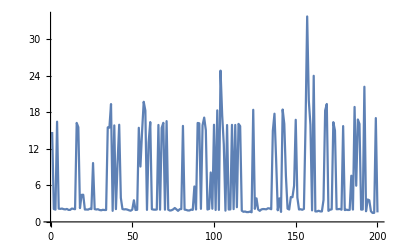

```mathematica
ListLinePlot[TimingData]
```

```mathematica
TimingData
```

{14.75,2.10938,2.01563,16.4375,2.17188,2.14063,2.1875,2.09375,2.04688,2.125,1.96875,1.96875,2.1875,2.14063,2.07813,16.2344,15.5313,2.26563,4.4375,4.45313,2.03125,2.03125,2.01563,2.15625,2.09375,9.65625,2.09375,2.03125,2.07813,1.95313,1.90625,1.98438,1.95313,1.95313,15.5156,20.625,19.3281,1.8125,20.4219,2.09375,9.625,21.5781,3.95313,2.10938,2.04688,2.07813,2.01563,1.90625,1.82813,2.01563,3.54688,1.95313,1.98438,21.4531,9.07813,20.0156,19.7031,18.2656,1.96875,12.9844,23.,2.07813,2.01563,2.,2.03125,23.7969,2.,23.0313,22.5313,2.,23.0313,2.,1.85938,1.90625,2.04688,2.28125,2.0625,1.8125,2.07813,2.10938,22.9688,2.01563,1.96875,1.875,1.875,2.01563,1.96875,5.8125,2.03125,23.1094,21.7188,2.14063,23.2031,25.2344,21.4063,2.03125,2.125,8.10938,2.15625,21.625,1.95313,30.4531,1.96875,23.8125,22.8594,12.6563,1.84375,21.7188,2.03125,2.04688,22.,2.09375,22.4844,2.40625,21.4688,22.4844,1.84375,1.65625,1.70313,1.60938,1.60938,1.6875,1.57813,18.3906,2.14063,3.85938,2.03125,1.8125,2.04688,2.10938,2.09375,2.0625,2.23438,2.20313,2.07813,21.625,21.3594,10.25,1.90625,3.85938,1.64063,33.2344,24.625,7.51563,2.17188,2.03125,4.07813,4.04688,5.9375,23.1094,3.98438,2.03125,2.07813,1.98438,2.125,15.8906,24.6563,19.8906,21.5469,1.89063,24.1406,1.71875,1.71875,1.82813,1.71875,1.71875,3.59375,18.2813,19.3438,1.8125,2.,2.0625,25.125,24.5156,2.07813,2.09375,2.125,2.,22.0156,1.9375,2.,1.95313,1.96875,7.57813,2.01563,18.8594,5.9375,16.7969,22.,2.01563,2.03125,22.1719,1.75,3.67188,3.54688,1.75,1.46875,1.48438,17.0313,1.5625}

### Plotting BoxPlots

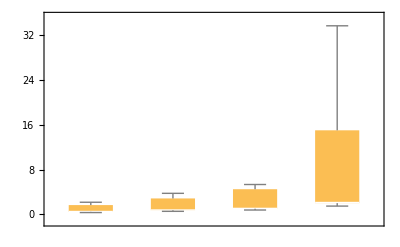

```mathematica
data2 = {TimingData20,TimingData30,TimingData40,TimingData60};
BoxWhiskerChart[data2]
```

### Plotting the Distribution of Timing Data

Median (n = 20) = 0.840885

Interquartile Spread (n = 20) = 0.259035

Interquartile Spread / Median (n = 20) = 0.30805

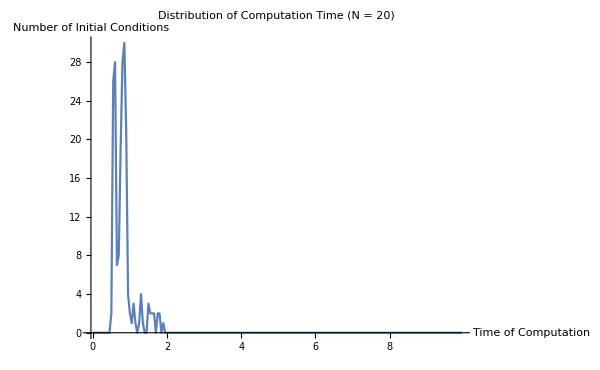

```mathematica
(* N = 20 *)

numberTests=Dimensions[TimingData20][[1]];
Tmax=10;
binLength=0.05;
epsilon=binLength/2;
numberBins=Tmax/binLength;
count20=ConstantArray[0,IntegerPart[numberBins]];
Print["Median (n = 20) = ",Median[TimingData20]];
Print["Interquartile Spread (n = 20) = ",InterquartileRange[TimingData20]];
Print["Interquartile Spread / Median (n = 20) = ",InterquartileRange[TimingData20] / Median[TimingData20]];
Table[Table[If[j*binLength-epsilon<=TimingData20[[i]]<=j*binLength+epsilon,count20[[j]]=count20[[j]]+1,_],{j,1,numberBins}];,{i,1,numberTests}];
xTicks=Table[{i,IntegerPart[(i-1)*binLength]},{i,1,IntegerPart[numberBins],IntegerPart[1/binLength]}];
ListLinePlot[count20,Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time (N = 20)"]
```

Median (n = 30) = 1.01112

Interquartile Spread (n = 30) = 0.250145

Interquartile Spread / Median (n = 30) = 0.247394

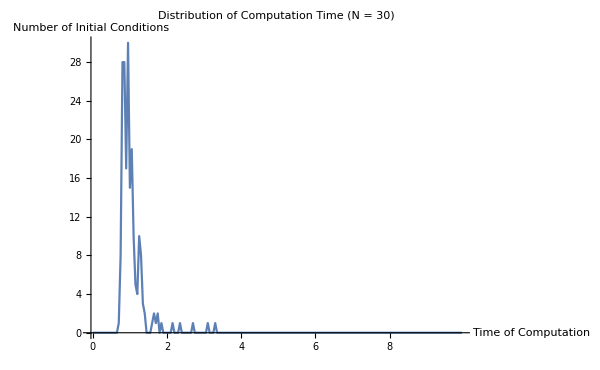

```mathematica
(* N = 30 *)

numberTests=Dimensions[TimingData30][[1]];
Tmax=10;
binLength=0.05;
epsilon=binLength/2;
numberBins=Tmax/binLength;
count30=ConstantArray[0,IntegerPart[numberBins]];
Print["Median (n = 30) = ",Median[TimingData30]];
Print["Interquartile Spread (n = 30) = ",InterquartileRange[TimingData30]];
Print["Interquartile Spread / Median (n = 30) = ",InterquartileRange[TimingData30] / Median[TimingData30]];
Table[Table[If[j*binLength-epsilon<=TimingData30[[i]]<=j*binLength+epsilon,count30[[j]]=count30[[j]]+1,_],{j,1,numberBins}];,{i,1,numberTests}];
xTicks=Table[{i,IntegerPart[(i-1)*binLength]},{i,1,IntegerPart[numberBins],IntegerPart[1/binLength]}];
ListLinePlot[count30,Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time (N = 30)"]
```

Median (n = 40) = 1.06005

Interquartile Spread (n = 40) = 0.171077

Interquartile Spread / Median (n = 40) = 0.235974

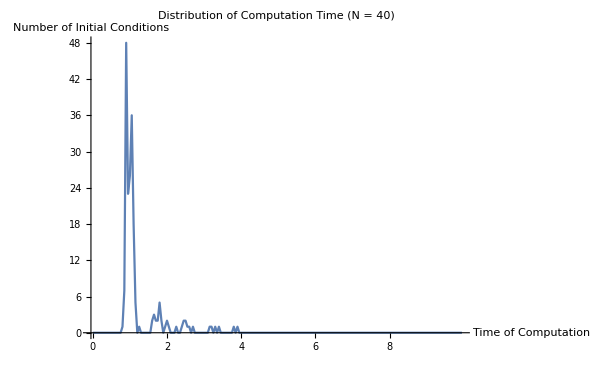

```mathematica
(* N = 40 *)

numberTests=Dimensions[TimingData40][[1]];
Tmax=10;
binLength=0.05;
epsilon=binLength/2;
numberBins=Tmax/binLength;
count40=ConstantArray[0,IntegerPart[numberBins]];
Print["Median (n = 40) = ",Median[TimingData40]];
Print["Interquartile Spread (n = 40) = ",InterquartileRange[TimingData40]];
Print["Interquartile Spread / Median (n = 40) = ",InterquartileRange[TimingData30] / Median[TimingData40]];
Table[Table[If[j*binLength-epsilon<=TimingData40[[i]]<=j*binLength+epsilon,count40[[j]]=count40[[j]]+1,_],{j,1,numberBins}];,{i,1,numberTests}];
xTicks=Table[{i,IntegerPart[(i-1)*binLength]},{i,1,IntegerPart[numberBins],IntegerPart[1/binLength]}];
ListLinePlot[count40,Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time (N = 40)"]
```

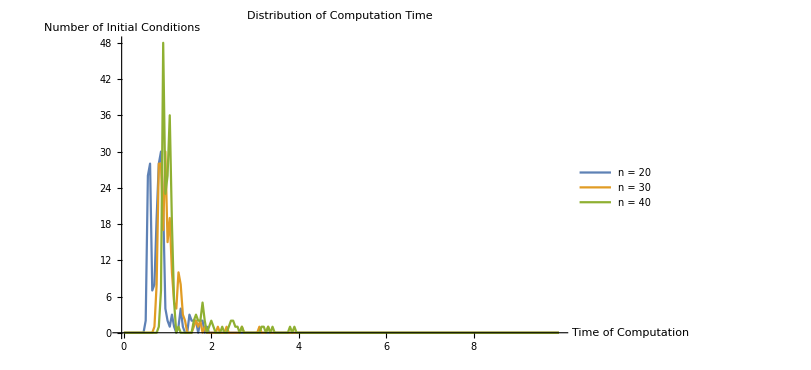

```mathematica
ListLinePlot[{count20,count30,count40},Ticks->{xTicks,Automatic},AxesLabel->{"Time of Computation","Number of Initial Conditions"},ImageSize->600,PlotLabel->"Distribution of Computation Time ",PlotLegends->{"n = 20","n = 30","n = 40"}]
```